```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["ErrorBarPlots`"]
Needs["ErrorBarLogPlots`"] (* this has to be installed separately*)
SE[x_]:=If[Length[x]>1,Sqrt[Variance[x]/Length[x]],0]
Clear[SEbin]
SEbin[data_]:=Module[{parts=Partition[data,UpTo[Floor[Length[data]/10]]],means},means=Mean[#]&/@parts;{Mean[1.data],SE[1.means]}]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Clear[WindowMean]
WindowMean[d_,n_]:=(Mean[#]&/@Partition[d,n]);
```

## Demonstration of replication synchrony loss

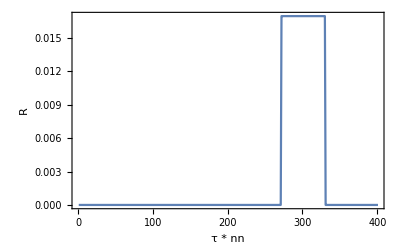

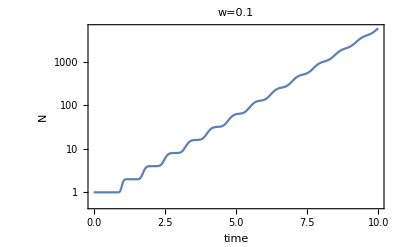

```mathematica
tmax=10;
nn=400;
Clear[p,rr,kk,n,norm]
(*p[i_]:=(i/nn)^2;*)
(*p[i_]:=Exp[-((i/nn)-0.7)^2/(2 0.03^2)];*)
(*rr[i_]:=Exp[-500.((i/nn)-0.75)^2];*)
www=0.1;
rr[i_]:=If[Abs[(i/nn)-0.75]<www 0.75,1,0];
norm=Sum[rr[i],{i,0,nn}];
ListPlot[Table[rr[i]/norm,{i,0,nn}],PlotRange->All,Joined->True,Frame->True,FrameLabel->{"τ * nn","R"}]
sol=NDSolve[Flatten[{
Table[D[n[i,t],t]==nn(-n[i,t]+If[i<nn,n[i+1,t],0])+2 nn n[0,t]rr[i]/norm,{i,1,nn}],
totn[t]==Sum[n[j,t],{j,0,nn}],
D[n[0,t],t]==nn (n[1,t]-n[0,t]),
Table[n[i,0]==If[i==nn,1,0],{i,0,nn}]}],
Flatten[{Table[n[i,t],{i,0,nn}],totn[t]}],{t,0,tmax}][[1]];
(*ListPlot[Table[Table[n[i,t],{i,0,nn}]/.sol,{t,0,tmax,tmax/4}],Joined->True,PlotRange->All]*)
ListLogPlot[Table[{t,totn[t]/.sol},{t,0,tmax,tmax/1000}],Joined->True,PlotRange->All,Frame->True,FrameLabel->{"time","N"},PlotLabel->"w="<>ToString[www],BaseStyle->FontSize->20,FrameStyle->Black]
```

## Figure 1

{f1'[t]==1. f1[t]+f1[t] Min[0,-7+(3 f2[t])/100000],f2'[t]==1. f2[t]+f2[t] Min[0,-f1[t]/100000+7 (1-f2[t]/1000000)],f1[0]==200000.,f2[0]==200000.}

{f1[t]→InterpolatingFunction[…][t],f2[t]→InterpolatingFunction[…][t]}

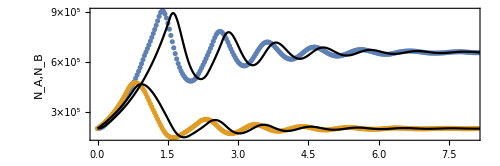

```mathematica
tmp=Import["data_30_7_7_10_b=1_k=1000000_nA02_nB02.dat","Table"];
tmax=12;
{f1'[t]==b f1[t]+f1[t]Min[p1 f2[t]/k-p2 ,0],f2'[t]==b f2[t]+f2[t]Min[p3 (1-f2[t]/k)-p4 (f1[t]/k),0],f1[0]==0.2k,f2[0]==0.2k}/.{p1->30,p2->7,p3->7,p4->10,b->1.,k->1000000}
sol=NDSolve[%,{f1[t],f2[t]},{t,0,tmax}][[1]]
{f1[t],f2[t]}/.sol;
Show[ListPlot[{tmp[[All,{1,2}]],tmp[[All,{1,3}]]},PlotRange->All],Plot[%,{t,0,tmax},PlotRange->All,PlotStyle->Black],PlotRange->{{0,8},All},AspectRatio->1/3,ImageSize->500,Frame->True,FrameStyle->Black,BaseStyle->FontSize->18,FrameTicks->{{{{0,"0"},{300000,"3×10^5"},{600000,"6×10^5"},{900000,"9×10^5"}},Automatic},{Automatic,Automatic}},FrameLabel->{"t","N_A,N_B"}]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig1b.pdf",%,"PDF"]
```

{1.2207,797423,293636}

{f1'[t]==1. f1[t]+f1[t] Min[0,-7+(3 f2[t])/100000],f2'[t]==1. f2[t]+f2[t] Min[0,-f1[t]/100000+7 (1-f2[t]/1000000)],f1[1.2207]==797423,f2[1.2207]==293636}

{f1[t]→InterpolatingFunction[…][t],f2[t]→InterpolatingFunction[…][t]}

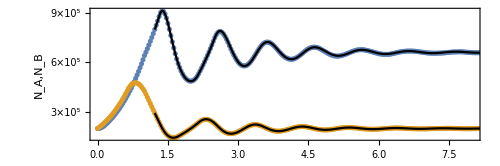

```mathematica
tmax=12;
nn=40;
tmp[[nn]]
{f1'[t]==b f1[t]+f1[t]Min[p1 f2[t]/k-p2 ,0],f2'[t]==b f2[t]+f2[t]Min[p3 (1-f2[t]/k)-p4 (f1[t]/k),0],f1[tmp[[nn,1]]]==tmp[[nn,2]],f2[tmp[[nn,1]]]==tmp[[nn,3]]}/.{p1->30,p2->7,p3->7,p4->10,b->1.,k->1000000}
sol=NDSolve[%,{f1[t],f2[t]},{t,tmp[[nn,1]],tmax}][[1]]
{f1[t],f2[t]}/.sol;
Show[ListPlot[{tmp[[All,{1,2}]],tmp[[All,{1,3}]]},PlotRange->All],Plot[%,{t,tmp[[nn,1]],tmax},PlotRange->All,PlotStyle->Black],PlotRange->{{0,8},All},AspectRatio->1/3,ImageSize->500,Frame->True,FrameStyle->Black,BaseStyle->FontSize->18,FrameTicks->{{{{0,"0"},{300000,"3×10^5"},{600000,"6×10^5"},{900000,"9×10^5"}},Automatic},{Automatic,Automatic}},FrameLabel->{"t","N_A,N_B"}]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig1c.pdf",%,"PDF"]
```

## Figure 2

```mathematica
asynchr=Import["S05_K_300000_1of_dev_002_tmax_10000\\S05_K_300000_1of_dev_005_tmax_10000_b_0.700000_e.dat"];
Length[asynchr]
```

32001

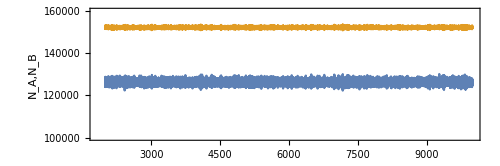

```mathematica
ListPlot[{asynchr[[All,{1,2}]],asynchr[[All,{1,3}]]},Frame->True,FrameLabel->{"t","N_A,N_B"},Joined->True,PlotRange->{100000,160000},FrameStyle->Black,BaseStyle->FontSize->18,AspectRatio->1/3,ImageSize->500]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig2a.pdf",%,"PDF"]
```

```mathematica
synchr=Import["S05_K_300000_1of_dev_002_tmax_10000\\S05_K_300000_1of_dev_005_tmax_10000_b_0.700000_s.dat"];
Length[synchr]
```

32001

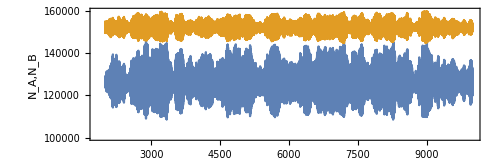

```mathematica
ListPlot[{synchr[[All,{1,2}]],synchr[[All,{1,3}]]},Frame->True,FrameLabel->{"t","N_A,N_B"},Joined->True,PlotRange->{100000,160000},FrameStyle->Black,BaseStyle->FontSize->18,AspectRatio->1/3,ImageSize->500]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig2b.pdf",%,"PDF"]
```

## Figure 3

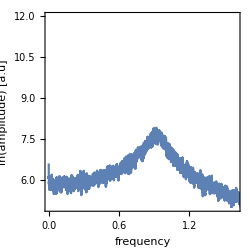

```mathematica
ListPlot[MovingAverage[Log[Abs[Fourier[asynchr[[All,2]]]]],20],PlotRange->{{0,1.6},{5,12}},Joined->True,DataRange->{0,Length[asynchr]/(asynchr[[-1,1]]-asynchr[[1,1]])},Frame->True,FrameLabel->{"frequency","ln(amplitude) [a.u]"},FrameStyle->Black,BaseStyle->FontSize->18,AspectRatio->1,ImageSize->250]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig3a.pdf",%,"PDF"]
```

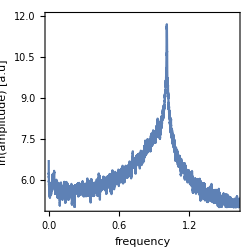

```mathematica
ListPlot[MovingAverage[Log[Abs[Fourier[synchr[[All,2]]]]],20],PlotRange->{{0,1.6},{5,12}},Joined->True,DataRange->{0,Length[synchr]/(synchr[[-1,1]]-synchr[[1,1]])},Frame->True,FrameLabel->{"frequency","ln(amplitude) [a.u]"},FrameStyle->Black,BaseStyle->FontSize->18,AspectRatio->1,ImageSize->250]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig3b.pdf",%,"PDF"]
```

## Figure 4

```mathematica
name="S05_K_100000_1of_dev_002_tmax_10000";
namese=FileNames[name<>"\\*_e.dat"];
namess=FileNames[name<>"\\*_s.dat"];
```

```mathematica
Clear[Maxamp]
Maxamp[d_]:=Max[d-Mean[d]]/Mean[d];
tmp=Table[Module[{de=ReadList[namese[[i]],{Number,Number,Number}],ds=ReadList[namess[[i]],{Number,Number,Number}]},{ToExpression[StringCases[namese[[i]],"b_"~~b__~~"_"->b][[1]]],StandardDeviation[1.de[[All,2]]]/Mean[1.de[[All,2]]],StandardDeviation[1.de[[All,3]]]/Mean[1.de[[All,3]]],StandardDeviation[1.ds[[All,2]]]/Mean[1.ds[[All,2]]],StandardDeviation[1.ds[[All,3]]]/Mean[1.ds[[All,3]]],Mean[1.de[[All,2]]],Mean[1.de[[All,3]]],Mean[1.ds[[All,2]]],Mean[1.ds[[All,3]]],Maxamp[1.de[[All,2]]],Maxamp[1.de[[All,3]]],Maxamp[1.ds[[All,2]]],Maxamp[1.ds[[All,3]]]}]
,{i,Length[namese]}];
```

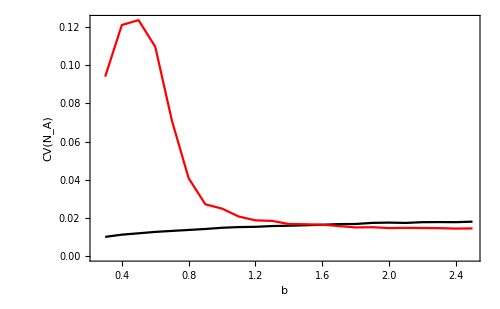

```mathematica
ListPlot[{tmp[[All,{1,2}]],tmp[[All,{1,4}]]},PlotRange->All,Joined->True,Frame->True,FrameStyle->Black,FrameLabel->{"b","CV(N_A)"},ImageSize->500,BaseStyle->FontSize->18,PlotStyle->{Black,Red}]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig4a.pdf",%,"PDF"]
```

```mathematica
Clear[ResPeak,tmp]
ResPeak[name_]:=Module[{namess=FileNames[name<>"\\*_s.dat"],ds,tmp,parts,means},
tmp=Table[ds=1.ReadList[namess[[i]],{Number,Number,Number}][[All,2]];(* only NA taken *)
parts=Select[Partition[ds,UpTo[Floor[Length[ds]/11]]],(Length[#]>1)&];means=(StandardDeviation[#]/Mean[#])&/@parts;{ToExpression[StringCases[namess[[i]],"b_"~~b__~~"_"->b][[1]]],StandardDeviation[ds]/Mean[ds],SE[means]}
,{i,Length[namess]}];
{{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&/@tmp
];
specs={ResPeak["S05_K_10000_1of_dev_002_tmax_50000"],ResPeak["S05_K_30000_1of_dev_002_tmax_50000"],ResPeak["S05_K_100000_1of_dev_002_tmax_50000"],ResPeak["S05_K_300000_1of_dev_002_tmax_10000"],ResPeak["S05_K_1000000_1of_dev_002_tmax_10000"]};
```

```mathematica
Length[#]&/@specs
```

{25,25,23,23,25}

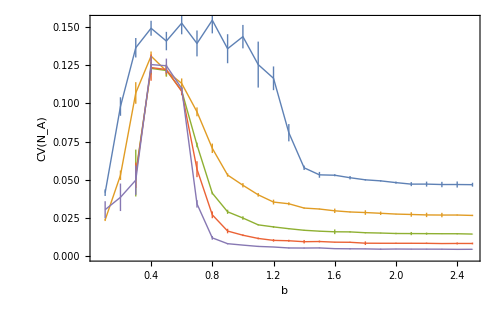

```mathematica
ErrorListPlot[specs,Joined->True,PlotRange->All,Frame->True,FrameStyle->Black,FrameLabel->{"b","CV(N_A)"},ImageSize->500,BaseStyle->FontSize->18,PlotStyle->Thick]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig4b.pdf",%,"PDF"]
```

```mathematica
specs2={ResPeak["S05_K_100000_1of_dev_002_tmax_50000"],ResPeak["S05_K_100000_1of_dev_004_tmax_10000"],ResPeak["S05_K_100000_1of_dev_008_tmax_10000"],ResPeak["S05_K_100000_1of_dev_01_tmax_10000"],ResPeak["S05_K_100000_1of_dev_02_tmax_10000"]};
Length[#]&/@specs2
```

{23,25,25,25,25}

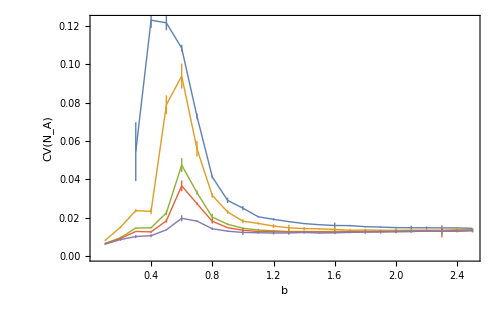

```mathematica
ErrorListPlot[specs2,Joined->True,PlotRange->All,Frame->True,FrameStyle->Black,FrameLabel->{"b","CV(N_A)"},ImageSize->500,BaseStyle->FontSize->18,PlotStyle->Thick]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig4c.pdf",%,"PDF"]
```

## Figure 5

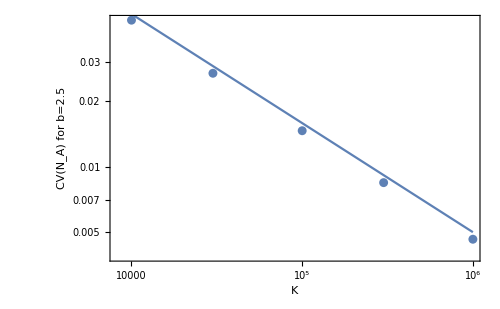

```mathematica
Show[ListLogLogPlot[{{10000,specs[[1,-1,1,2]]},{30000,specs[[2,-1,1,2]]},{100000,specs[[3,-1,1,2]]},{300000,specs[[4,-1,1,2]]},{1000000,specs[[5,-1,1,2]]}}],LogLogPlot[5/x^0.5,{x,10000,1000000}],Frame->True,FrameStyle->Black,FrameLabel->{"K","CV(N_A) for b=2.5"},ImageSize->500,BaseStyle->FontSize->18]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig5.pdf",%,"PDF"]
```

## Figure 6

```mathematica
tmp=Join[Import[NotebookDirectory[]<>"\\P_extinction\\runs_quasi\\runs_details.dat","Table"],Import[NotebookDirectory[]<>"\\P_extinction\\runs_exponential\\runs_details.dat","Table"][[2;;]]];
```

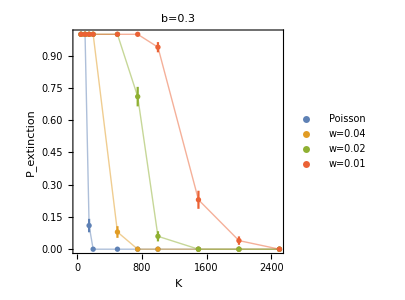

```mathematica
wws={1,0.04,0.02,0.01};
pext=Table[Sort[({{Mean[#[[All,6]]],p},ErrorBar[Sqrt[p(1-p)/Length[#]]]}/.p->1.Mean[#[[All,1]]])&/@Gather[Select[tmp,(#[[7]]==ww && #[[5]]==0.3 && #[[6]]<3000)&],(#1[[6]]==#2[[6]])&]],{ww,wws}];
Show[ListPlot[pext[[All,All,1]],Joined->True,PlotStyle->{{Opacity[0.5],Thick}}],ErrorListPlot[pext,PlotRange->All,LabelStyle->Directive[FontSize->14],PlotLegends->Placed[{"Poisson","w=0.04","w=0.02","w=0.01"},{0.75,0.7}]],Frame->True,FrameStyle->Black,FrameLabel->{"K","P_extinction"},ImageSize->300,BaseStyle->FontSize->18,AspectRatio->1,PlotLabel->"b=0.3"]
Export[NotebookDirectory[]<>"\\fig6a.pdf",%,"PDF"]
```

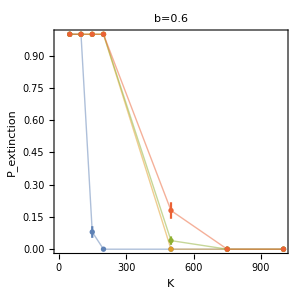

```mathematica
wws={1,0.04,0.02,0.01};
pext=Table[Sort[({{Mean[#[[All,6]]],p},ErrorBar[Sqrt[p(1-p)/Length[#]]]}/.p->1.Mean[#[[All,1]]])&/@Gather[Select[tmp,(#[[7]]==ww && #[[5]]==0.6 && #[[6]]<1200)&],(#1[[6]]==#2[[6]])&]],{ww,wws}];
Show[ListPlot[pext[[All,All,1]],Joined->True,PlotStyle->{{Opacity[0.5],Thick}}],ErrorListPlot[pext,PlotRange->All(*,PlotLegends->{("w="<>ToString[#])&/@wws}*)],Frame->True,FrameStyle->Black,FrameLabel->{"K","P_extinction"},ImageSize->300,BaseStyle->FontSize->18,AspectRatio->1,PlotLabel->"b=0.6"]
Export[NotebookDirectory[]<>"\\fig6b.pdf",%,"PDF"]
```

```mathematica
tmpsurv=Select[tmp,(#[[1]]==0)&];
tmpext=Select[tmp,(#[[1]]==1)&];
```

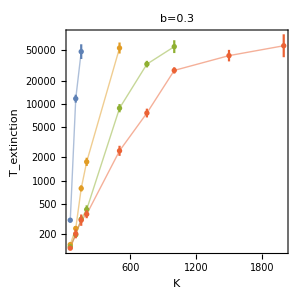

```mathematica
wws={1,0.04,0.02,0.01};
bbb=0.3;
Textinct=Table[ttt=Sort[({{Mean[#[[All,6]]],Mean[#[[All,4]]]},ErrorBar[SE[#[[All,4]]]]})&/@Gather[Select[tmpext,(#[[7]]==ww && #[[5]]==bbb)&],(#1[[6]]==#2[[6]])&]];If[Length[ttt]>0,ttt,{{{0,10^5},ErrorBar[0]}}],{ww,wws}];
Show[ListLogPlot[Textinct[[All,All,1]],Joined->True,PlotStyle->{{Opacity[0.5],Thick}}],ErrorListLogPlot[Textinct,PlotRange->All,LabelStyle->Directive[FontSize->14](*,PlotLegends->Placed[{("w="<>ToString[#])&/@wws},{Center,Right}]*)],Frame->True,FrameStyle->Black,FrameLabel->{"K","T_extinction"},ImageSize->300,BaseStyle->FontSize->18,PlotLabel->("b="<>ToString[bbb]),PlotRange->All,AspectRatio->1,FrameTicks->{{{{Log[100],"10^2"},{Log[1000],"10^3"},{Log[10000],"10^4"},{Log[100000],"10^5"}},Automatic},{Automatic,Automatic}}]
Export[NotebookDirectory[]<>"\\fig6c.pdf",%,"PDF"]
```

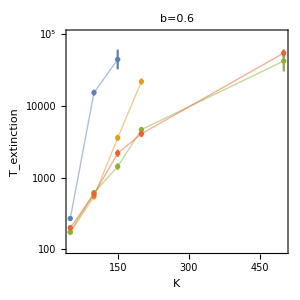

```mathematica
wws={1,0.04,0.02,0.01};
bbb=0.6;
Textinct=Table[ttt=Sort[({{Mean[#[[All,6]]],Mean[#[[All,4]]]},ErrorBar[SE[#[[All,4]]]]})&/@Gather[Select[tmpext,(#[[7]]==ww && #[[5]]==bbb)&],(#1[[6]]==#2[[6]])&]];If[Length[ttt]>0,ttt,{{{0,10^5},ErrorBar[0]}}],{ww,wws}];
Show[ListLogPlot[Textinct[[All,All,1]],Joined->True,PlotStyle->{{Opacity[0.5],Thick}}],ErrorListLogPlot[Textinct,PlotRange->All,LabelStyle->Directive[FontSize->14](*,PlotLegends->Placed[{("w="<>ToString[#])&/@wws},{Center,Right}]*)],Frame->True,FrameStyle->Black,FrameLabel->{"K","T_extinction"},ImageSize->300,BaseStyle->FontSize->18,PlotLabel->("b="<>ToString[bbb]),PlotRange->{Log[100],Log[10^5]},AspectRatio->1,FrameTicks->{{{{Log[100],"10^2"},{Log[1000],"10^3"},{Log[10000],"10^4"},{Log[100000],"10^5"}},Automatic},{Automatic,Automatic}}]
Export[NotebookDirectory[]<>"\\fig6d.pdf",%,"PDF"]
```

## Figure 7

```mathematica
devs={"0.02","0.04","0.2"};
bbs={"0.3","0.6"};
kks={"100","200","500","1000","2000","5000"};

Clear[GetBaseFreq]
GetBaseFreq[d_]:=Module[{fft=Abs[Fourier[d]][[2;;Floor[Length[d]/2]]]},Ordering[fft,-1][[1]]]
Clear[variances]
variances={};
Do[
Do[
Do[
names=FileNames["time_series_quasi\\kk_"<>kks[[k]]<>"\\bb_"<>bbs[[j]]<>"\\dev_"<>devs[[i]]<>"\\rep_*\\populations.dat"];
If[Length[names]>0,
vars=Table[nabs=1.Select[ReadList[names[[i]],{Number,Number,Number},5000],(#[[2]]!=0 && #[[3]]!=0)&];
nmax=GetBaseFreq[nabs[[All,2]]];{Variance[nabs[[All,2]]],Variance[nabs[[All,3]]],Mean[nabs[[All,2]]],Mean[nabs[[All,3]]],Mean[Sort[nabs[[All,2]]][[1;;nmax]]]},{i,Length[names]}];
Print["kk=",kks[[k]]," bb=",bbs[[j]]," dev=",devs[[i]]," ln(vars)=",Length[vars]];
AppendTo[variances,{ToExpression[kks[[k]]],ToExpression[bbs[[j]]],ToExpression[devs[[i]]],   Mean[vars[[All,1]]],Mean[vars[[All,2]]],SE[vars[[All,1]]],SE[vars[[All,2]]], Mean[vars[[All,3]]],Mean[vars[[All,4]]],SE[vars[[All,3]]],SE[vars[[All,4]]],  Mean[vars[[All,5]]]}];
];
,{j,Length[bbs]}],{i,Length[devs]}],{k,Length[kks]}]
```

kk=100 bb=0.3 dev=0.02 ln(vars)=21

kk=100 bb=0.6 dev=0.02 ln(vars)=21

kk=100 bb=0.3 dev=0.04 ln(vars)=21

kk=100 bb=0.6 dev=0.04 ln(vars)=21

kk=100 bb=0.3 dev=0.2 ln(vars)=21

kk=100 bb=0.6 dev=0.2 ln(vars)=21

kk=200 bb=0.3 dev=0.02 ln(vars)=21

kk=200 bb=0.6 dev=0.02 ln(vars)=21

kk=200 bb=0.3 dev=0.04 ln(vars)=21

kk=200 bb=0.6 dev=0.04 ln(vars)=21

kk=200 bb=0.3 dev=0.2 ln(vars)=20

kk=200 bb=0.6 dev=0.2 ln(vars)=20

kk=500 bb=0.3 dev=0.02 ln(vars)=21

kk=500 bb=0.6 dev=0.02 ln(vars)=20

kk=500 bb=0.3 dev=0.04 ln(vars)=21

kk=500 bb=0.6 dev=0.04 ln(vars)=20

kk=500 bb=0.3 dev=0.2 ln(vars)=20

kk=500 bb=0.6 dev=0.2 ln(vars)=20

kk=1000 bb=0.3 dev=0.02 ln(vars)=21

kk=1000 bb=0.6 dev=0.02 ln(vars)=20

kk=1000 bb=0.3 dev=0.04 ln(vars)=20

kk=1000 bb=0.6 dev=0.04 ln(vars)=20

kk=1000 bb=0.3 dev=0.2 ln(vars)=20

kk=1000 bb=0.6 dev=0.2 ln(vars)=20

kk=2000 bb=0.3 dev=0.02 ln(vars)=20

kk=2000 bb=0.6 dev=0.02 ln(vars)=20

kk=2000 bb=0.3 dev=0.04 ln(vars)=20

kk=2000 bb=0.6 dev=0.04 ln(vars)=20

kk=2000 bb=0.3 dev=0.2 ln(vars)=20

kk=2000 bb=0.6 dev=0.2 ln(vars)=20

kk=5000 bb=0.3 dev=0.02 ln(vars)=20

kk=5000 bb=0.6 dev=0.02 ln(vars)=20

kk=5000 bb=0.3 dev=0.04 ln(vars)=20

kk=5000 bb=0.6 dev=0.04 ln(vars)=20

kk=5000 bb=0.3 dev=0.2 ln(vars)=20

kk=5000 bb=0.6 dev=0.2 ln(vars)=20

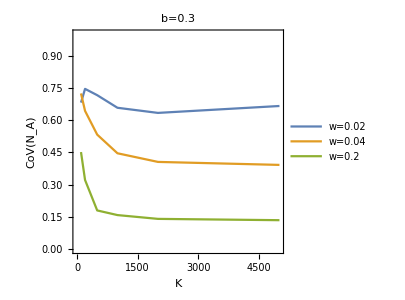

```mathematica
wws={0.02,0.04,0.2};
ListPlot[Table[{#[[1]],Sqrt[#[[4]]]/#[[8]]}&/@Select[variances,(#[[2]]==0.3 && #[[3]]==ww)&],{ww,wws}],LabelStyle->Directive[FontSize->14],PlotLegends->Placed[{("w="<>ToString[#])&/@wws},{0.75,0.8}],Frame->True,FrameStyle->Black,FrameLabel->{"K","CoV(N_A)"},ImageSize->300,BaseStyle->FontSize->18,PlotLabel->("b=0.3"),PlotRange->{0,1},AspectRatio->1,Joined->True]
Export[NotebookDirectory[]<>"\\fig7a.pdf",%,"PDF"]
```

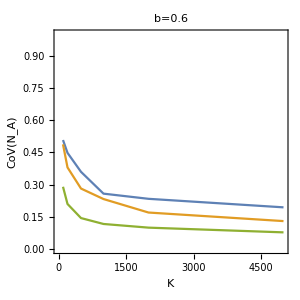

```mathematica
ListPlot[Table[{#[[1]],Sqrt[#[[4]]]/#[[8]]}&/@Select[variances,(#[[2]]==0.6 && #[[3]]==ww)&],{ww,wws}],LabelStyle->Directive[FontSize->14](*,PlotLegends->Placed[{("w="<>ToString[#])&/@wws},{Center,Right}]*),Frame->True,FrameStyle->Black,FrameLabel->{"K","CoV(N_A)"},ImageSize->300,BaseStyle->FontSize->18,PlotLabel->("b=0.6"),PlotRange->{0,1},AspectRatio->1,Joined->True]
Export[NotebookDirectory[]<>"\\fig7b.pdf",%,"PDF"]
```

## Figure 8

```mathematica
asynchr=ReadList["one_species_k=100000_e.dat",{Number,Number}];
Length[asynchr]

synchr=ReadList["K=100000_tmax=10000_n0=1\\K=100000_tmax=10000_n0=1_dev_0.02_s.dat",{Number,Number}];
Length[synchr]
```

320001

1108798

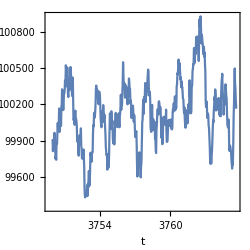

```mathematica
ListPlot[asynchr[[120000;;120500]],PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","n"},AspectRatio->1,FrameStyle->Black,ImageSize->250,BaseStyle->FontSize->18]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig8a.pdf",%,"PDF"]
```

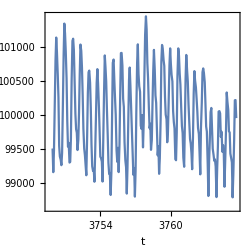

```mathematica
ListPlot[synchr[[60000;;60250]],PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","n"},AspectRatio->1,FrameStyle->Black,ImageSize->250,BaseStyle->FontSize->18]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig8b.pdf",%,"PDF"]
```

```mathematica
names=({{"K=100000_tmax=1000_dt10_tmax=10000_save16\\K=100000_tmax=1000_dt10_tmax=10000_save16_dev_0.02_s.dat"}, {"K=100000_tmax=1000_dt10_tmax=10000_save16\\K=100000_tmax=1000_dt10_tmax=10000_save16_dev_0.04_s.dat"}, {"K=100000_tmax=1000_dt10_tmax=10000_save16\\K=100000_tmax=1000_dt10_tmax=10000_save16_dev_0.05_s.dat"}, {"K=100000_tmax=1000_dt10_tmax=10000_save16\\K=100000_tmax=1000_dt10_tmax=10000_save16_dev_0.08_s.dat"}, {"K=100000_tmax=1000_dt10_tmax=10000_save16\\K=100000_tmax=1000_dt10_tmax=10000_save16_dev_0.1_s.dat"}, {"K=100000_tmax=1000_dt10_tmax=10000_save16\\K=100000_tmax=1000_dt10_tmax=10000_save16_dev_0.2_s.dat"}, {"K=100000_tmax=1000_dt10_tmax=10000_save16\\K=100000_tmax=1000_dt10_tmax=10000_save16_dev_0_s.dat"}, {"K=100000_tmax=1000_dt10_tmax=10000_save16\\K=100000_tmax=1000_dt10_tmax=10000_save16_exp.dat"}});
```

```mathematica
data=Module[{tmp=ReadList[#,{Number,Number}],ind={1}},Do[If[tmp[[i,1]]<tmp[[i-1,1]],AppendTo[ind,i]],{i,2,Length[tmp]}];AppendTo[ind,Length[tmp]+1];Table[tmp[[ind[[n]];;ind[[n+1]]-1]],{n,Length[ind]-1}]]&/@names;
Table[Length[#]&/@data[[k]],{k,8}]
```

{{640001,640001,640001,444766},{640001,640001,640001,427179},{640001,640001,640001,436354},{640001,640001,640001,434503},{640001,640001,640001,425864},{640001,640001,640001,435193},{640001,640001,640001,435617},{640001,640001,640001,416736}}

```mathematica
sss={0.02 ,0.04 ,0.05 ,0.08 ,0.1 ,0.2 ,0,1 (* this is exp case *)};
If[Length[data]≠Length[sss],Interrupt[]];
stddevs=Table[Module[{d=Table[StandardDeviation[1.data[[i,j,Floor[0.5Length[data[[i,j]]]];;,2]]],{j,Length[data[[i]]]}]},{sss[[i]],Mean[d],StandardDeviation[d]}],{i,Length[data]}]
```

{{0.02,721.644,41.5601},{0.04,365.191,7.44453},{0.05,332.004,3.8815},{0.08,279.463,3.81513},{0.1,263.658,2.29668},{0.2,246.214,2.9314},{0,15934.8,443.456},{1,315.793,3.18978}}

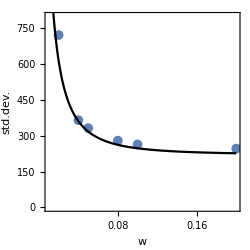

```mathematica
Show[ListPlot[{#[[1]],#[[2]]}&/@stddevs,PlotStyle->AbsolutePointSize[7],Frame->True,AspectRatio->1,FrameLabel->{"w","std.dev."},FrameStyle->Black,ImageSize->250,BaseStyle->FontSize->18],Plot[ Sqrt[10^5](0.9241962407465939(1/(4Log[2]^2.)+(π^2 (12-6 Coth[Log[2]/2] Log[2]+Log[2]^2))/(12 γ Log[2]^4)/.{(*γ->decay[ϵ]*)γ->(28.5/3)(w)^2}))^0.5,{w,0.01,0.2},PlotRange->{0,All},PlotStyle->Black],PlotRange->{{0.01,0.2},{0,800}}]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig8c.pdf",%,"PDF"]
```

```mathematica
Expand[(0.9241962407465939(1/(4Log[2]^2.)+(π^2 (12-6 Coth[Log[2]/2] Log[2]+Log[2]^2))/(12 γ Log[2]^4)))]
```

0.480898+0.0125255/γ

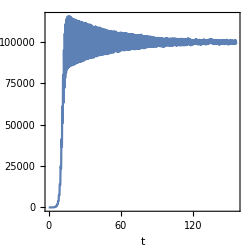

```mathematica
ListPlot[data[[3,1,1;;10000]],PlotRange->All,AspectRatio->1,Joined->True,Frame->True,FrameLabel->{"t","n"},FrameStyle->Black,ImageSize->250,BaseStyle->FontSize->18]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig8d.pdf",%,"PDF"]
```

### this code estimated the rate of exponential decay of oscillations from the time series data, for different w=0.02,...0.2

```mathematica
decays={};
```

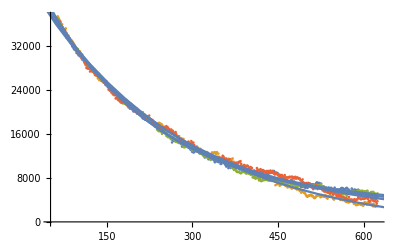

```mathematica
Module[{fun=a+b Exp[-c t],slopes,d=Table[{Mean[#[[All,1]]],Max[#[[All,2]]]-Min[#[[All,2]]]}&/@Partition[data[[1,i,4000;;40000]],80],{i,Length[data[[1]]]}]},fit=Table[FindFit[d[[i]],fun,{{a,0},{b,30000},{c,0.005}},t],{i,Length[d]}];slopes=(c)/.fit;AppendTo[decays,{0.02,Mean[slopes],SE[slopes]}];Print[Show[ListPlot[d,PlotRange->All],Plot[fun/.fit,{t,0,1500},PlotRange->All]]];]
```

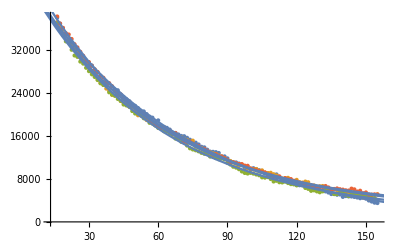

```mathematica
Module[{fun=a+b Exp[-c t],slopes,d=Table[{Mean[#[[All,1]]],Max[#[[All,2]]]-Min[#[[All,2]]]}&/@Partition[data[[2,i,1000;;10000]],80],{i,Length[data[[2]]]}]},fit=Table[FindFit[d[[i]],fun,{{a,0},{b,30000},{c,0.005}},t],{i,Length[d]}];slopes=(c)/.fit;AppendTo[decays,{0.04,Mean[slopes],SE[slopes]}];Print[Show[ListPlot[d,PlotRange->All],Plot[fun/.fit,{t,0,1500},PlotRange->All]]];]
```

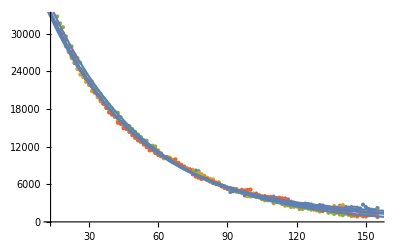

```mathematica
Module[{fun=a+b Exp[-c t],slopes,d=Table[{Mean[#[[All,1]]],Max[#[[All,2]]]-Min[#[[All,2]]]}&/@Partition[data[[3,i,1000;;10000]],80],{i,Length[data[[3]]]}]},fit=Table[FindFit[d[[i]],fun,{{a,0},{b,30000},{c,0.005}},t],{i,Length[d]}];slopes=(c)/.fit;AppendTo[decays,{0.05,Mean[slopes],SE[slopes]}];Print[Show[ListPlot[d,PlotRange->All],Plot[fun/.fit,{t,0,1500},PlotRange->All]]];]
```

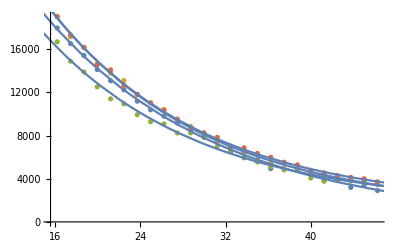

```mathematica
Module[{fun=a+b Exp[-c t],slopes,d=Table[{Mean[#[[All,1]]],Max[#[[All,2]]]-Min[#[[All,2]]]}&/@Partition[data[[4,i,1000;;3000]],80],{i,Length[data[[4]]]}]},fit=Table[FindFit[d[[i]],fun,{{a,0},{b,30000},{c,0.02}},t],{i,Length[d]}];slopes=(c)/.fit;AppendTo[decays,{0.08,Mean[slopes],SE[slopes]}];Print[Show[ListPlot[d,PlotRange->All],Plot[fun/.fit,{t,0,1500},PlotRange->All]]];]
```

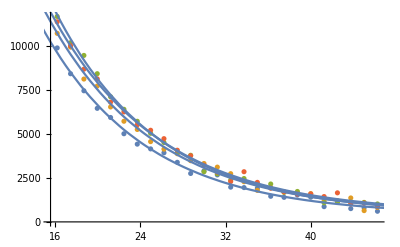

```mathematica
Module[{fun=a+b Exp[-c t],slopes,d=Table[{Mean[#[[All,1]]],Max[#[[All,2]]]-Min[#[[All,2]]]}&/@Partition[data[[5,i,1000;;3000]],80],{i,Length[data[[5]]]}]},fit=Table[FindFit[d[[i]],fun,{{a,0},{b,30000},{c,0.02}},t],{i,Length[d]}];slopes=(c)/.fit;AppendTo[decays,{0.1,Mean[slopes],SE[slopes]}];Print[Show[ListPlot[d,PlotRange->All],Plot[fun/.fit,{t,0,1500},PlotRange->All]]];]
```

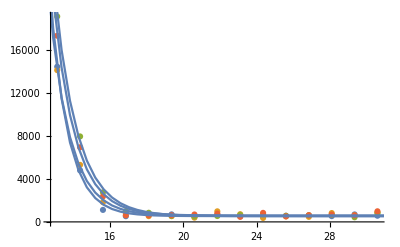

```mathematica
Module[{fun=a+b Exp[-c t],slopes,d=Table[{Mean[#[[All,1]]],Max[#[[All,2]]]-Min[#[[All,2]]]}&/@Partition[data[[6,i,800;;2000]],80],{i,Length[data[[6]]]}]},fit=Table[FindFit[d[[i]],fun,{{a,0},{b,30000},{c,0.02}},t],{i,Length[d]}];slopes=(c)/.fit;AppendTo[decays,{0.2,Mean[slopes],SE[slopes]}];Print[Show[ListPlot[d,PlotRange->All],Plot[fun/.fit,{t,0,1500},PlotRange->All]]];]
```

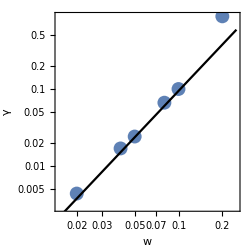

```mathematica
Show[ErrorListLogLogPlot[{{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&/@decays,PlotRange->{{0.015,0.25},All},PlotStyle->AbsolutePointSize[10]],LogLogPlot[9.5 ϵ^2,{ϵ,0.01,0.25},PlotStyle->Black],Frame->True,AspectRatio->1,FrameLabel->{"w","γ"},FrameStyle->Black,ImageSize->250,BaseStyle->FontSize->18]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig8e.pdf",%,"PDF"]
```

## Figure S1

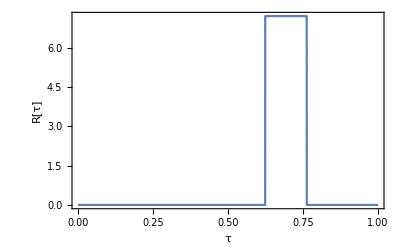

1.00116

```mathematica
Clear[nstar]
rr[τ_]:=If[Abs[τ-Log[2]]<0.1Log[2],1/(2 0.1Log[2]),0]
Plot[rr[τ],{τ,0,1},Frame->True,FrameLabel->{"τ","R[τ]"},BaseStyle->FontSize->20]
nstar[τ_,j_]:=1.0012Exp[j τ](1-2NIntegrate[Exp[-j τp]rr[τp],{τp,0,τ}])
jj=j/.FindRoot[Integrate[Exp[-j τ]rr[τ],{τ,0,1}]==1/2,{j,1.}]
```

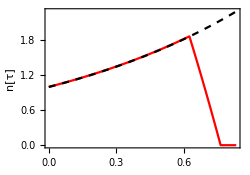

```mathematica
Plot[{nstar[τ,jj],Exp[τ]},{τ,0,1.2Log[2]},PlotStyle->{Red,{Black,Dashed}},Frame->True,FrameLabel->{"τ","n[τ]"},FrameStyle->Black,BaseStyle->FontSize->18,AspectRatio->0.7,ImageSize->250]
```

```mathematica
Export[NotebookDirectory[]<>"\\figS1.pdf",%,"PDF"]
```

## Figure S2

### determine the frequency spectrum for time series for different w' s use moving average to smooth out the spectra

```mathematica
flen=5 1.45;
specs=Table[Sum[Module[{d=data[[i,j,Floor[Min[Length[#]&/@data[[i]]]/4];;Min[Length[#]&/@data[[i]]],2]],n,dt=Mean[Differences[data[[i,j,1;;100,1]]]],tmax},n=Length[d];tmax=dt n;d-=Mean[d];(* this is the same formula as for the 2-species model *)(Abs[Fourier[d]][[2;;Floor[flen n dt]]])^2(dt)],{j,Length[data[[i]]]}]/Length[data[[i]]],{i,Length[data]}];
```

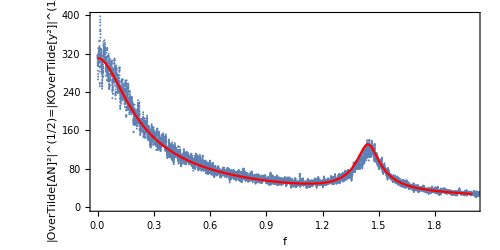

```mathematica
Show[ListPlot[MovingAverage[specs[[6,2;;]]^0.5,10],DataRange->{0,flen},PlotRange->{{0,2},All}],Plot[Sqrt[10^5]Sqrt[(dd2/(ω^2+1))+1/((ω-2π/Log[2])^2+γ^2)(2Log[2]^2dd2)/((2π)^2+Log[2]^2)]/.{dd2->0.962,γ->(28.5/3)(0.2)^2}/.ω->2π f,{f,0,2},PlotRange->{0,All},PlotStyle->Red],Frame->True,AspectRatio->0.5,FrameLabel->{"f","|OverTilde[ΔN]^2|^(1/2)=|KOverTilde[y^2]|^(1/2)"},FrameStyle->Black,ImageSize->500,BaseStyle->FontSize->18]
```

```mathematica
Export[NotebookDirectory[]<>"\\figS2a.pdf",%,"PDF"]
```

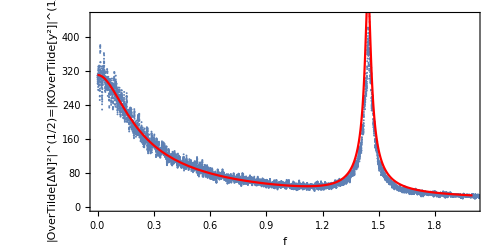

```mathematica
Show[ListPlot[MovingAverage[specs[[5,2;;]]^0.5,10],DataRange->{0,flen},PlotRange->{{0,2},All}],Plot[Sqrt[10^5]Sqrt[(dd2/(ω^2+1))+1/((ω-2π/Log[2])^2+γ^2)(2Log[2]^2dd2)/((2π)^2+Log[2]^2)]/.{dd2->0.962,γ->(28.5/3)(0.1)^2}/.ω->2π f,{f,0,2},PlotRange->{0,All},PlotStyle->Red],Frame->True,AspectRatio->0.5,FrameLabel->{"f","|OverTilde[ΔN]^2|^(1/2)=|KOverTilde[y^2]|^(1/2)"},FrameStyle->Black,ImageSize->500,BaseStyle->FontSize->18]
```

```mathematica
Export[NotebookDirectory[]<>"\\figS2b.pdf",%,"PDF"]
```

```mathematica
(dd2/(ω^2+1))+1/((ω-2π/Log[2])^2+γ^2)(2Log[2]^2dd2)/((2π)^2+Log[2]^2)/.{dd2->0.962}/.ω->2π f
```

0.962/(1+4 f^2 π^2)+0.0231336/(γ^2+(2 f π-(2 π)/Log[2])^2)

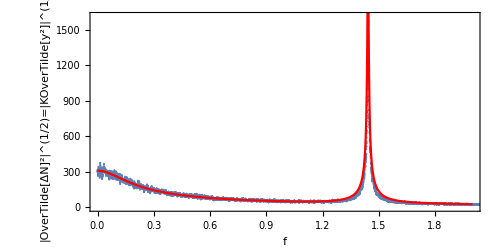

```mathematica
Show[ListPlot[MovingAverage[specs[[3,2;;]]^0.5,10],DataRange->{0,flen},PlotRange->{{0,2},All}],Plot[Sqrt[10^5]Sqrt[(dd2/(ω^2+1))+1/((ω-2π/Log[2])^2+γ^2)(2Log[2]^2dd2)/((2π)^2+Log[2]^2)]/.{dd2->0.962,γ->(28.5/3)(0.05)^2}/.ω->2π f,{f,0,2},PlotRange->{0,All},PlotStyle->Red],Frame->True,AspectRatio->0.5,FrameLabel->{"f","|OverTilde[ΔN]^2|^(1/2)=|KOverTilde[y^2]|^(1/2)"},FrameStyle->Black,ImageSize->500,BaseStyle->FontSize->18]
```

```mathematica
Export[NotebookDirectory[]<>"\\figS2c.pdf",%,"PDF"]
```

## Figure 9

```mathematica
asynchr=Import["S05_K_100000_1of_exp_tmax_10000_dt10_save16\\S05_K_100000_1of_exp_tmax_10000_dt10_save16_b_1.000000_e.dat"];
```

0.015625

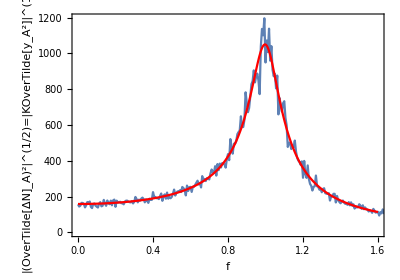

```mathematica
Module[{p=(* S05 *){39.73,20.86,2.,4.}(* S02 {56.45488229193919,29.227441145969596,0.8,2.8}*),b=1.0,kk=100000,dt,tt,nn},
dt=1.(asynchr[[-1,1]]-asynchr[[1,1]])/Length[asynchr];
(*tt=(asynchr[[-1,1]]-asynchr[[1,1]]);nn=Length[asynchr];*)
Print[dt];
Show[ListPlot[Sqrt[WindowMean[(Abs[Fourier[asynchr[[All,2]]]][[2;;]])^2dt,50]],PlotRange->{{0,1.6},{0,All}},Joined->True,DataRange->{0,1/dt},Frame->True,FrameLabel->{"f","|(OverTilde[ΔN]_A)^2|^(1/2)=|KOverTilde[y_A^2]|^(1/2)"},FrameStyle->Black,BaseStyle->FontSize->18,AspectRatio->0.7,ImageSize->400],pl=Plot[Sqrt[(a22^2 η1^2-2 a12 a22 (0)+a12^2 η2^2+η1^2 ω^2)/(a12^2 a21^2+2 a12 a21 ω^2+a22^2 ω^2+ω^4)]/.{η1^2->2b kk/2,η2^2->2b kk/2 ,a12->((b-p[[2]])p[[3]]+p[[1]](b+p[[3]]))/p[[4]],a22->p[[3]]/p[[1]](b-p[[2]]),a21->p[[4]]/p[[1]](b-p[[2]])}/.ω->2π f,{f,0,1.6},PlotRange->All,PlotStyle->Red]]]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig9.pdf",%,"PDF"]
```

## Figure 10

```mathematica
synchr2=Import["S05_K_100000_1of_dev_008_tmax_10000_dt10_save16\\S05_K_100000_1of_dev_008_tmax_10000_dt10_save16_b_0.900000_s.dat"][[4000;;-1]];
Length[synchr2]
```

508002

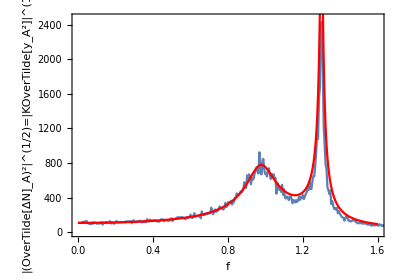

```mathematica
Module[{p=(* S05 *){39.73,20.86,2.,4.}(* S02 {56.45488229193919,29.227441145969596,0.8,2.8}*),b=0.9,ka=47000,kb=50000,dt,dd,tt},
dt=(synchr2[[-1,1]]-synchr2[[1,1]])/Length[synchr2];
Show[ListPlot[Sqrt[WindowMean[(Abs[Fourier[synchr2[[All,2]]]][[2;;]])^2(dt),40]],PlotRange->{{0,1.6},{0,All}},Joined->True,DataRange->{0,1/dt},Frame->True,FrameLabel->{"f","|(OverTilde[ΔN]_A)^2|^(1/2)=|KOverTilde[y_A^2]|^(1/2)"},FrameStyle->Black,BaseStyle->FontSize->18,AspectRatio->0.7,ImageSize->400],pl=Plot[Sqrt[(a22^2 η1^2-2 a12 a22(0 η1^2)+a12^2 η2^2+η1^2 ω^2)/(a12^2 a21^2+2 a12 a21 ω^2+a22^2 ω^2+ω^4)]/.η2^2->(kb/ka) η1^2/.{η1^2-> ka((b^2+ω^2)dd2(1/((Log[2]/tt)^2+ω^2)+(2  Log[2]^2)/(( γ^2+(ω-2 π/tt)^2) (4 π^2+Log[2]^2)))/.{dd2->0.962,tt->Log[2]/b,γ->6.579(b/0.69)(0.08)^2}),a12->((b-p[[2]])p[[3]]+p[[1]](b+p[[3]]))/p[[4]],a22->p[[3]]/p[[1]](b-p[[2]]),a21->p[[4]]/p[[1]](b-p[[2]])}/.ω->2π (f-0.00),{f,0,1.6},PlotRange->All,PlotStyle->Red]]]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig10a.pdf",%,"PDF"]
```

```mathematica
synchr=Import["S05_K_100000_1of_dev_008_tmax_10000_dt10_save16\\S05_K_100000_1of_dev_008_tmax_10000_dt10_save16_b_0.700000_s.dat"];
Length[synchr]
```

512001

0.015625

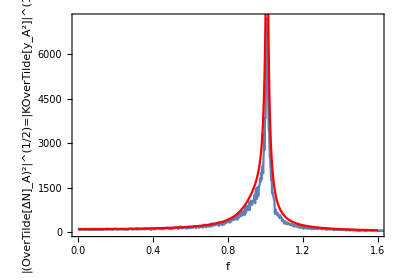

```mathematica
Module[{p=(* S05 *){39.73,20.86,2.,4.}(* S02 {56.45488229193919,29.227441145969596,0.8,2.8}*),b=0.7,ka=42000,kb=51000,dt,dd,tt,γ},
dt=1.(synchr[[-1,1]]-synchr[[1,1]])/Length[synchr];Print[dt];
Show[ListPlot[Sqrt[WindowMean[(Abs[Fourier[synchr[[All,2]]]][[2;;]])^2(dt ),20]],PlotRange->{{0,1.6},{0,All}},Joined->True,DataRange->{0,1/dt},Frame->True,FrameLabel->{"f","|(OverTilde[ΔN]_A)^2|^(1/2)=|KOverTilde[y_A^2]|^(1/2)"},FrameStyle->Black,BaseStyle->FontSize->18,AspectRatio->0.7,ImageSize->400],
pl=Plot[Sqrt[(a22^2 η1^2-2 a12 a22(0 η1^2)+a12^2 η2^2+η1^2 ω^2)/(a12^2 a21^2+2 a12 a21 ω^2+a22^2 ω^2+ω^4)]/.η2^2->(kb/ka)η1^2/.{η1^2-> ka((b^2+ω^2)dd2(1/((Log[2]/tt)^2+ω^2)+(2 tt^2 Log[2]^2)/((tt^2 γ^2+(-2 π+tt ω)^2) (4 π^2+Log[2]^2)))/.{dd2->0.962,tt->1,γ->6.579(0.08)^2}),a12->((b-p[[2]])p[[3]]+p[[1]](b+p[[3]]))/p[[4]],a22->p[[3]]/p[[1]](b-p[[2]]),a21->p[[4]]/p[[1]](b-p[[2]])}/.ω->2π (f-0.008),{f,0,1.6},PlotRange->All,PlotStyle->Red]]]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig10b.pdf",%,"PDF"]
```

## Figure 11

### variances for different w:

```mathematica
Clear[VarianceNA]
VarianceNA[name_]:=Module[{namess=FileNames[name<>"\\*_s.dat"],ds,tmp,parts,means},
tmp=Table[ds=1.ReadList[namess[[i]],{Number,Number,Number}][[All,2]];(* only NA taken *)
parts=Partition[ds,UpTo[Floor[Length[ds]/11]]];means=Variance[#]&/@parts;{ToExpression[StringCases[namess[[i]],"b_"~~b__~~"_"->b][[1]]],Variance[ds],SE[means]}
,{i,Length[namess]}];
{{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&/@tmp
]
```

```mathematica
vars={VarianceNA["S05_K_100000_1of_dev_004_tmax_10000"],VarianceNA["S05_K_100000_1of_dev_008_tmax_10000"],VarianceNA["S05_K_100000_1of_dev_01_tmax_10000"],VarianceNA["S05_K_100000_1of_dev_02_tmax_10000"]};
vvv=vars[[All,7]]
vvv[[All,1,1]]={(*0.02,*)0.04,0.08,0.1,0.2};
```

{{{0.7,5.55038×10^6},ErrorBar[1.0495×10^6]},{{0.7,1.94925×10^6},ErrorBar[121683.]},{{0.7,1.33489×10^6},ErrorBar[63263.5]},{{0.7,598964.},ErrorBar[29792.]}}

{{0.04,1.01154×10^7},{0.06,4.59455×10^6},{0.08,2.66063×10^6},{0.1,1.76398×10^6},{0.12,1.27563×10^6},{0.14,980174.},{0.16,787727.},{0.18,655402.},{0.2,560632.}}

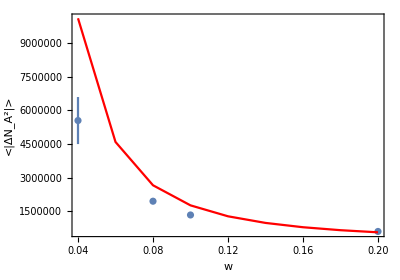

```mathematica
vvtheor=Table[{ww,Module[{p=(* S05 *){39.73,20.86,2.,4.}(* S02 {56.45488229193919,29.227441145969596,0.8,2.8}*),b=0.69,kk=10^5,dt,meanna,meannb,tt,dd,expr,γ},
meanna=-(-b kk p[[1]]-b kk p[[3]]-kk p[[1]] p[[3]]+kk p[[2]] p[[3]])/(p[[1]] p[[4]]);
meannb=-(b kk-kk p[[2]])/p[[1]];
expr=(1/(2π))(a22^2 η1^2-2 a12 a22(0 )+a12^2 η2^2+η1^2 ω^2)/(a12^2 a21^2+2 a12 a21 ω^2+a22^2 ω^2+ω^4)/.η2^2-> η1^2(meannb/meanna)/.{η1^2-> (meanna)((b^2+ω^2)dd2(1/((Log[2]/tt)^2+ω^2)+(2 tt^2 Log[2]^2)/((tt^2 γ^2+(-2 π+tt ω)^2) (4 π^2+Log[2]^2)))/.{dd2->0.962,tt->Log[2]/b,γ->6.579(b/0.69)(ww)^2}),a12->((b-p[[2]])p[[3]]+p[[1]](b+p[[3]]))/p[[4]],a22->p[[3]]/p[[1]](b-p[[2]]),a21->p[[4]]/p[[1]](b-p[[2]])};
Re[NIntegrate[
expr,{ω,-150,150},MaxRecursion->20,MinRecursion->10]]]},{ww,0.04,0.2,0.02}]
Show[ErrorListPlot[vvv],ListPlot[vvtheor,Joined->True,PlotStyle->Red],PlotRange->All,Frame->True,FrameLabel->{"w","<|ΔN_A^2|>"},FrameStyle->Black,BaseStyle->FontSize->18,AspectRatio->0.7,ImageSize->400]
```

```mathematica
Export[NotebookDirectory[]<>"\\fig11.pdf",%,"PDF"]
```